```mathematica
Quit[]
```

# Setup

```mathematica
<<SNEG`
```

sneg 1.234 Copyright (C) 2013 Rok Zitko

sneg.m $Id: sneg.m,v 1.234 2013/09/24 07:47:24 rokzitko Exp rokzitko $ loaded

```mathematica
<<Mypackage`
```

```mathematica
<<MaTeX`
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{simplewick}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{simplewick}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
ScriptGen[{γ},{1,2,3,4,5}]
```

```mathematica
ψbr[f_,x_,lrntz_:"",clr_:""]/:MakeBoxes[ψbr[f_,x_,lrntz_:"",clr_:""],TraditionalForm]:=SubsuperscriptBox[OverscriptBox[ToBoxes[f,TraditionalForm],StyleBox["_",Bold]],RowBox[{ToBoxes[x,TraditionalForm],ToBoxes[lrntz,TraditionalForm]}],ToBoxes[clr,TraditionalForm]]
```

```mathematica
ψ[f_,x_,lrntz_:"",clr_:""]/:MakeBoxes[ψ[f_,x_,lrntz_:"",clr_:""],TraditionalForm]:=SubsuperscriptBox[ToBoxes[f,TraditionalForm],RowBox[{ToBoxes[x,TraditionalForm],ToBoxes[lrntz,TraditionalForm]}],ToBoxes[clr,TraditionalForm]]
```

```mathematica
WL[z1_,z2_,a_:"",b_:""]/:MakeBoxes[WL[z1_,z2_,a_:"",b_:""],TraditionalForm]:=SubsuperscriptBox["W",RowBox[{ToBoxes[z1,TraditionalForm],";",ToBoxes[z2,TraditionalForm]}],RowBox[{ToBoxes[a,TraditionalForm],ToBoxes[b,TraditionalForm]}]]
```

```mathematica
S[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""]/:MakeBoxes[S[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""],TraditionalForm]:=SubsuperscriptBox[RowBox[{"(",SubsuperscriptBox["S",ToBoxes[x1←x2,TraditionalForm],ToBoxes[q,TraditionalForm]],")"}],RowBox[{RowBox[{ToBoxes[lrntz1,TraditionalForm],ToBoxes[lrntz2,TraditionalForm]}]}],RowBox[{ToBoxes[clr1,TraditionalForm],ToBoxes[clr2,TraditionalForm]}]]
```

```mathematica
Sdg[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""]/:MakeBoxes[Sdg[q_,x1_,x2_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""],TraditionalForm]:=SubsuperscriptBox[SuperscriptBox[RowBox[{"(",SubsuperscriptBox["S",ToBoxes[x1←x2,TraditionalForm],ToBoxes[q,TraditionalForm]],")"}],StyleBox["†",Bold]],RowBox[{RowBox[{ToBoxes[lrntz1,TraditionalForm],ToBoxes[lrntz2,TraditionalForm]}]}],RowBox[{ToBoxes[clr1,TraditionalForm],ToBoxes[clr2,TraditionalForm]}]]
```

```mathematica
(*tt=ψbr[u,f].γ5.ψ[d,f].ψbr[u,x+z].WL[x+z,x].γ3.ψ[u,x].ψbr[u,y].γ2.ψ[u,r].ψ[u,i].γ5.ψbr[d,i]*)
```

```mathematica
OprtrsTeX[Oprtrs_]:=StringReplace[#,"\\overset{\\_}"->"\\overline"]&/@(ToString/@TeXForm/@List@@Oprtrs);
```

```mathematica
Cntrctn2TeX[FldOprtrs_,OPsCntedUnsrt_List]:=Module[{Ops=StringReplace[#,"\\overset{\\_}"->"\\overline"]&/@(ToString/@TeXForm/@List@@FldOprtrs),OPsCnted=Sort/@OPsCntedUnsrt,len=Length[OPsCntedUnsrt],CntedOPs,CntedOPs1,itmp},CntedOPs=Table[Ops⟦#⟧&/@{1;;OPsCnted⟦itmp,1⟧-1,OPsCnted⟦itmp,1⟧;;OPsCnted⟦itmp,1⟧,OPsCnted⟦itmp,1⟧+1;;OPsCnted⟦itmp,2⟧-1,OPsCnted⟦itmp,2⟧;;OPsCnted⟦itmp,2⟧},{itmp,1,len}];CntedOPs1=Table[{(Mod[jtmp,2]*"\\acontraction["+Mod[jtmp+1,2]"\\bcontraction[")<>ToString[IntegerPart[(jtmp+1)/2]]<>"ex]"}~Join~#&[(Map["{"<>StringJoin@@#<>"}"&,CntedOPs,{2}])⟦jtmp⟧],{jtmp,1,len}];StringJoin@@({(StringJoin@@CntedOPs1)<>"  "}~Join~{Ops})]
```

```mathematica
CntndFlds[FldOprtrs_Dot]:=Module[{FldOprtrsLst=List@@FldOprtrs,FrmnFldLst},FrmnFldLst=Union[Select[FldOprtrsLst,MemberQ[{ψ,ψbr},Head[#]]&]//.{ψbr[fld_,___]:>fld,ψ[fld_,___]:>fld}];FrmnFldLst]
```

```mathematica
FndCntrct[FldOprtrs_]:=SortBy[Join@@Module[{itmp,FldOprtrsLst=List@@FldOprtrs,Flds=CntndFlds[FldOprtrs]},Table[SortBy[#,Head[#]]&/@DeleteCases[Subsets[Flatten[Select[FldOprtrsLst,((MemberQ[{ψ,ψbr},Head[#]]&&(#//.{ψbr[fld_,___]:>fld,ψ[fld_,___]:>fld})==Flds⟦itmp⟧)&)]],{2}],_?(Count[#,ψ[_,___]]≠Count[#,ψbr[_,___]]&)],{itmp,1,Length[Flds]}]],First]
```

```mathematica
GrpdCntrctd[FldOprtrs_]:=Module[{OprtrsFnd=FndCntrct[FldOprtrs]},Select[Subsets[SortBy[OprtrsFnd,First],{Length[GroupBy[SortBy[OprtrsFnd,First],First]]}],DuplicateFreeQ[Flatten[#,1]]&]]
```

```mathematica
GrpdCntrctdIndx[FldOprtrs_]:=Module[{OprtrsFnd=FndCntrct[FldOprtrs]},Map[Sort,Map[Position[FldOprtrs,#]⟦1,1⟧&,Select[Subsets[SortBy[OprtrsFnd,First],{Length[GroupBy[SortBy[OprtrsFnd,First],First]]}],DuplicateFreeQ[Flatten[#,1]]&],{3}],2]]
```

```mathematica
ShwCntrctn[FldOprtrs_,nColscale_:{1,2}]:=Module[{indx=GrpdCntrctdIndx[FldOprtrs],lngth},lngth=Length[indx];Grid[ArrayReshape[MaTeX[Cntrctn2TeX[FldOprtrs,#],Magnification->nColscale⟦2⟧]&/@indx,{IntegerPart[lngth/nColscale⟦1⟧]+1,nColscale⟦1⟧},""]]]
```

```mathematica
ToPrpgtrs[exp_]:=exp//.{{ψ[q_,x1_,lrntz1_:"",clr1_:""],ψbr[q_,x2_,lrntz2_:"",clr2_:""]}:>S[q,x1,x2,lrntz1,lrntz2,clr1,clr2],{ψbr[q_,x1_,lrntz1_:"",clr1_:""],ψ[q_,x2_,lrntz2_:"",clr2_:""]}:>Sdg[q,x2,x1,lrntz2,lrntz1,clr2,clr1]}
```

```mathematica
CntrctSgn[pairs_]:=Module[{optr,lngth=Length[pairs],optrlst,mom,ncd},snegfermionoperators[optr];optrlst=DeleteCases[Flatten[(SparseArray[Flatten[MapIndexed[{#1⟦1⟧->((optr[First[#2]+1])[AN,mom[First[#2]]]),#1⟦2⟧->((optr[First[#2]+1])[CR,mom[First[#2]]])}&,pairs]]]//Normal)],0];ncd=(nc@@optrlst)//.δ[_]->0;ncd/(ncd//.-x_:>x)]
```

```mathematica
γ5[α_,β_]/:MakeBoxes[γ5[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(",ToBoxes[γ5,TraditionalForm],")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
γ3[α_,β_]/:MakeBoxes[γ3[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(",ToBoxes[γ3,TraditionalForm],")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
ScriptGen[{α,β,c},{f,i}]
```

```mathematica
Γ[α_,β_]/:MakeBoxes[Γ[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(","Γ",")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
Γdg[α_,β_]/:MakeBoxes[Γdg[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(",SuperscriptBox["Γ",StyleBox["†",Bold]],")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

```mathematica
P[α_,β_]/:MakeBoxes[P[α_,β_],TraditionalForm]:=SubscriptBox[RowBox[{"(","P",")"}],RowBox[{ToBoxes[α,TraditionalForm],ToBoxes[β,TraditionalForm]}]]
```

# π correlation ⟨(π̄(f))_α(π(i))_α⟩

```mathematica
πOprtrs=ψbr[d,i,αi,ci].γ5[αi,βi].ψ[u,i,βi,ci].ψbr[u,f,αf,cf].γ5[αf,βf].ψ[d,f,βf,cf]
```

(d̄)_(i α_i)^c_i.(γ_5)_(α_i β_i).u_(i β_i)^c_i.(ū)_(f α_f)^c_f.(γ_5)_(α_f β_f).d_(f β_f)^c_f

```mathematica
ShwCntrctn[πOprtrs,{1,1.5}]
```

-Graphics-

```mathematica
πgrphs=GrpdCntrctd[πOprtrs]//.{ψbr[fld_,pos_,___]:>pos,ψ[fld_,pos_,___]:>pos};
```

```mathematica
πgrphs
```

({f,i} | {i,f})

```mathematica
Rule@@#&/@πgrphs⟦1⟧
```

{f→i,i→f}

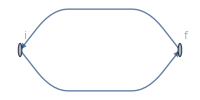

```mathematica
Graph[(Rule@@@πgrphs⟦1⟧),EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

```mathematica
ToPrpgtrs[GrpdCntrctd[πOprtrs]]
```

((S_(f←i)^d)_(β_f α_i)^(c_f c_i) | (S_(i←f)^u)_(β_i α_f)^(c_i c_f))

```mathematica
πOprtrs
```

(d̄)_(i α_i)^c_i.(γ_5)_(α_i β_i).u_(i β_i)^c_i.(ū)_(f α_f)^c_f.(γ_5)_(α_f β_f).d_(f β_f)^c_f

```mathematica
Dot@@Flatten[{γ5[αi,βi]}~Join~ToPrpgtrs[GrpdCntrctd[πOprtrs]]~Join~{γ5[αf,βf]}]
```

```mathematica
πrslt=Dot@@Flatten[{γ5[αi,βi]}~Join~ToPrpgtrs[GrpdCntrctd[πOprtrs]]~Join~{γ5[αf,βf]}]//.{S[q_,x1_,f,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""]:>Sdg[q,f,x1,lrntz1,lrntz2,clr1,clr2],S[q_,i,x1_,lrntz1_:"",lrntz2_:"",clr1_:"",clr2_:""]:>Sdg[q,x1,i,lrntz1,lrntz2,clr1,clr2]}
```

(γ_5)_(α_i β_i).(S_(f←i)^d)_(β_f α_i)^(c_f c_i).((S_(f←i)^u)^†)_(β_i α_f)^(c_i c_f).(γ_5)_(α_f β_f)

```mathematica
πrslt⟦4⟧.πrslt⟦2⟧.πrslt⟦1⟧.πrslt⟦3⟧
```

(γ_5)_(α_f β_f).(S_(f←i)^d)_(β_f α_i)^(c_f c_i).(γ_5)_(α_i β_i).((S_(f←i)^u)^†)_(β_i α_f)^(c_i c_f)

```mathematica
CntrctSgn[GrpdCntrctdIndx[πOprtrs]]
```

-1

# Nucleon correlation ⟨(N̄(f))_α(N(i))_α⟩, case1

```mathematica
ScriptGen[{i,f}]
```

```mathematica
ScriptGen[{a,b,c,α,β,ρ,μ,ν},{i,f}]
```

```mathematica
NOprtrs=ψ[d,f,β',b'].Γ[β',α'].ψ[u,f2,α',a'].ψ[u,f1,γ',c'].P[γ',γ].ψbr[u,i1,γ,c].ψbr[u,i2,α,a].Γ[α,β].ψbr[d,i,β,b]
```

d_(f β')^b'.(Γ)_(β' α').u_(f^2 α')^a'.u_(f^1 γ')^c'.(P)_(γ' γ).(ū)_(i^1 γ)^c.(ū)_(i^2 α)^a.(Γ)_αβ.(d̄)_iβ^b

```mathematica
ShwCntrctn[NOprtrs//.{i1->i,i2->i,f1->f,f2->f},{1,1.5}]
```

-Graphics-
-Graphics-

```mathematica
Ngrphs=GrpdCntrctd[NOprtrs]//.{ψbr[fld_,pos_,___]:>pos,ψ[fld_,pos_,___]:>pos};
```

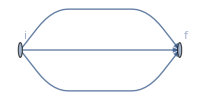

```mathematica
Graph[(Rule@@@Ngrphs⟦1⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

```mathematica
Graph[(Rule@@@Ngrphs⟦2⟧)//.{i1->i,i2->i,f1->f,f2->f},EdgeShapeFunction->({Arrowheads[{{.05,0.5}}],Arrow[Reverse[#]]}&),VertexLabels->"Name",ImageSize->{200,100},AspectRatio->1/2]
```

-Graphics-

```mathematica
Nrslt1=Times@@Flatten[{Γ[β',α'],P[γ',γ],Γ[α,β]}~Join~ToPrpgtrs[GrpdCntrctd[NOprtrs//.{i1->i,i2->i,f1->f,f2->f}]⟦1⟧]];
```

```mathematica
Nrslt2=Times@@Flatten[{Γ[β',α'],P[γ',γ],Γ[α,β]}~Join~ToPrpgtrs[GrpdCntrctd[NOprtrs//.{i1->i,i2->i,f1->f,f2->f}]⟦2⟧]];
```

```mathematica
CntrctSgn/@GrpdCntrctdIndx[NOprtrs]
```

{1,-1}

```mathematica
(Nrslt1-Nrslt2)//FullSimplify
```

(Γ)_αβ (P)_(γ' γ) (Γ)_(β' α') (S_(f←i)^d)_(β' β)^(b' b) ((S_(f←i)^u)_(α' α)^(a' a) (S_(f←i)^u)_(γ' γ)^(c' c)-(S_(f←i)^u)_(α' γ)^(a' c) (S_(f←i)^u)_(γ' α)^(c' a))

```mathematica
γE[2].γE
```